# Textually Describing Wolfram Language Expressions

Renan Germano

Mackenzie Presbyterian University, Brazil

## Goal

The objective of the present project is to create a function to textually describe Wolfram Language expressions.This is done by developing an algorithm that is capable of better describing the input, based on its symbolic structure, where the output is a human readable String.Thinking about accessibility for visually impaired, this text could be used as an automatically generated alternative description for graphics and related content.

## Describing colors

RGB color | ToString | TextString | SpokenString | Description
RGBColor[{0.13834638211441952, 0.10944037874548829, 0.09705518183954887}] | RGBColor[{0.138346, 0.10944, 0.0970552}] | RGBColor[{0.138346, 0.10944, 0.0970552}] | RGB color 0.138, 0.109, 0.097 | Black
RGBColor[{0.6998114874500838, 0.013106753310190289, 0.7453896078041529}] | RGBColor[{0.699811, 0.0131068, 0.74539}] | RGBColor[{0.699811, 0.0131068, 0.74539}] | RGB color 0.7, 0.013, 0.745 | Purple
RGBColor[{0.41098744104091556, 0.8671517747586834, 0.6623246833367291}] | RGBColor[{0.410987, 0.867152, 0.662325}] | RGBColor[{0.410987, 0.867152, 0.662325}] | RGB color 0.411, 0.867, 0.662 | Light Green
RGBColor[{0.6371560959968514, 0.7985979800330758, 0.2571355735647842}] | RGBColor[{0.637156, 0.798598, 0.257136}] | RGBColor[{0.637156, 0.798598, 0.257136}] | RGB color 0.637, 0.799, 0.257 | Light Green
RGBColor[{0.548304732640936, 0.725850133023968, 0.1819235574702489}] | RGBColor[{0.548305, 0.72585, 0.181924}] | RGBColor[{0.548305, 0.72585, 0.181924}] | RGB color 0.548, 0.726, 0.182 | Green
RGBColor[{0.8818156401069392, 0.47620256378328363, 0.10674904138416186}] | RGBColor[{0.881816, 0.476203, 0.106749}] | RGBColor[{0.881816, 0.476203, 0.106749}] | RGB color 0.882, 0.476, 0.107 | Orange
RGBColor[{0.29500412829881206, 0.9079955791864953, 0.7014883513816168}] | RGBColor[{0.295004, 0.907996, 0.701488}] | RGBColor[{0.295004, 0.907996, 0.701488}] | RGB color 0.295, 0.908, 0.701 | Light Green
RGBColor[{0.43979550971980985, 0.3546381234991267, 0.012921790905866759}] | RGBColor[{0.439796, 0.354638, 0.0129218}] | RGBColor[{0.439796, 0.354638, 0.0129218}] | RGB color 0.44, 0.355, 0.013 | Gray
RGBColor[{0.10609572752463148, 0.9630025658230474, 0.8666665284503903}] | RGBColor[{0.106096, 0.963003, 0.866667}] | RGBColor[{0.106096, 0.963003, 0.866667}] | RGB color 0.106, 0.963, 0.867 | Cyan
RGBColor[{0.8443134928309199, 0.9344760613670275, 0.11019104425074921}] | RGBColor[{0.844313, 0.934476, 0.110191}] | RGBColor[{0.844313, 0.934476, 0.110191}] | RGB color 0.844, 0.934, 0.11 | Yellow

RGB Color | English | Spanish | Portuguese | Japanese
RGBColor[{0.5315508423688435, 0.8963071160423999, 0.08447860222293757}] | Light Green | verde claro | verde claro | 薄緑色
RGBColor[{0.8562436874347557, 0.893878676250859, 0.9084928333204632}] | White | blanco | branco | 白
RGBColor[{0.078990535524045, 0.2047584826132307, 0.9728208319859564}] | Blue | azul | azul | 青
RGBColor[{0.13184733619671873, 0.3559323783015158, 0.9632163441824413}] | Blue | azul | azul | 青
RGBColor[{0.32261583418055184, 0.6428518478739196, 0.2411705809881679}] | Green | verde | verde | 緑
RGBColor[{0.903279482578941, 0.29128764519587347, 0.9627255998789606}] | Magenta | magenta | magenta | マジェンタ色
RGBColor[{0.33752208400869743, 0.14683940761731473, 0.21909170395070832}] | Black | negro | preto | 黒
RGBColor[{0.4460312710483445, 0.6652266938300524, 0.7588244456181577}] | Light Blue | azul claro | azul claro | 水色
RGBColor[{0.10859052562981009, 0.42251186083727865, 0.2091899403102908}] | Green | verde | verde | 緑
RGBColor[{0.22433340366812882, 0.9301433802623331, 0.6934793545924998}] | Light Green | verde claro | verde claro | 薄緑色

## Describing graphics

Graphics | ToString | TextString | SpokenString | Description
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0.5, 0.5 and Triangle of the list the list 0, 0, the list 2, 0, the list 3 halves, 1 half times square root of 3 | A graphic consisting of light pink triangle.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0.5, 0.5, edge form thickness Large and Triangle of the list the list 0, 0, the list 1, 0, the list 3 fourths, 1 fourth times square root of 3 | A graphic consisting of light pink triangle.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0, 0 and AffineHalfSpace of the list 0, 0, the list the list 1, minus 1 and the list 1, 1 | A graphic consisting of red affine half space.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0, 1, 0 and AffineSpace of the list 0, 0 and the list the list 1, minus 1 | A graphic consisting of light green affine space.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0.5, 0.5 and Annulus of the list 0, 0 and the list 1 half, 1 | A graphic consisting of light pink annulus.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of an arrow | A graphic consisting of red arrow.

## Describing triangles

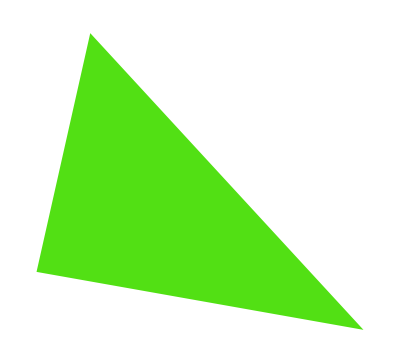
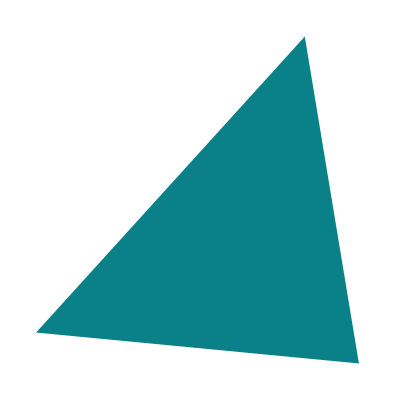
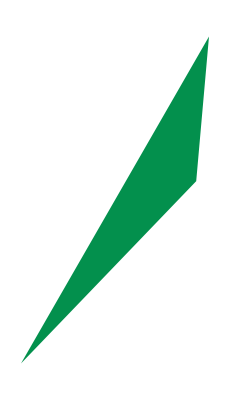
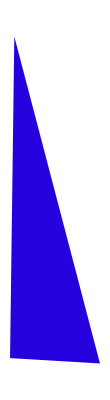
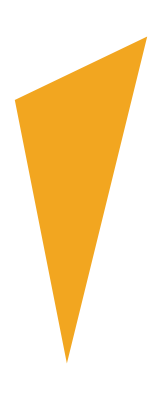
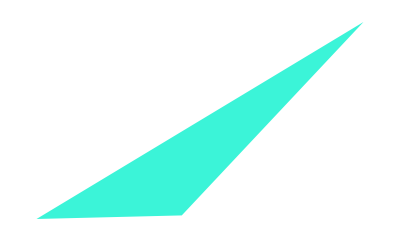
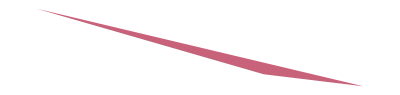
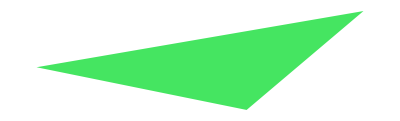
Graphics | ToString | TextString | SpokenString | TriangleDescription
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a light green, scalene triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a gray, scalene triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a green, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a blue, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a orange, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a cyan, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a light pink, scalene and obtuse triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a light green, scalene and obtuse triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a light pink, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a green, scalene and obtuse triangle, with its greatest side as a diagonal line.